```mathematica
N[10^ZetaZero[1]]
```

1.34784+2.86065 ⅈ

```mathematica
N[ExpIntegralEi[(1-ZetaZero[1]) Log[10]]]
```

0.0880046-3.10063 ⅈ

```mathematica
N[-Gamma[0, -(1-ZetaZero[1]) Log[10]]]-Pi I
```

0.0880046-3.10063 ⅈ

```mathematica
N[-Sum[1/j(1- Gamma[ j,-ZetaZero[1]Log[10]]/Gamma[j]),{j,1,1360}]]
```

-4.54189+1.57113 ⅈ

```mathematica
N[LogIntegral[10^ZetaZero[1]]]
```

1.97481+2.7126 ⅈ

```mathematica
N[-Sum[1/j( (Gamma[ j,0,-(1-ZetaZero[1])Log[10]]-Pi I)/Gamma[j]),{j,1,1360}]]
```

-4.54219+3.8269 ⅈ

```mathematica
fp[n_,a_]:=Sum[ ((a^(1-ZetaZero[1]))^k-1)/k,{k,1,Log[a,n]}]+Log[(1-ZetaZero[1])Log[n]]+EulerGamma
```

```mathematica
fp[10,1.0001]
```

0.0879872-3.09999 ⅈ

```mathematica
se[n_,a_,s_] := Sum[ ((a^(1-s))^k-1)/k,{k,1,Log[a,n]}]
```

```mathematica
s=N[ZetaZero[1]];{se[nn=10,1.00001,s]+EulerGamma+Log[(1-s)Log[nn]],N[ExpIntegralEi[(1-s)Log[nn]]],-Gamma[0,-(1-s)Log[nn]]- Pi I}
```

{0.0880018-3.10056 ⅈ,0.0880046-3.10063 ⅈ,0.0880046-3.10063 ⅈ}

```mathematica
se[10,1.00001,N[ZetaZero[1]]]+EulerGamma+Log[(1-ZetaZero[1]) Log[10]]
```

0.0880018-3.10056 ⅈ

```mathematica
N[ExpIntegralEi[(1-ZetaZero[1])Log[10]]]
```

0.0880046-3.10063 ⅈ

```mathematica
Limit[ (Gamma[a,0,-Log[n^(1-ZetaZero[1])]]/Gamma[a] - 1)/a,{a->0}]
```

{-Gamma[0,-Log[n^(1-ZetaZero[1])]]}

```mathematica
Limit[ (Gamma[a,0,-(1-ZetaZero[1])Log[n]]/Gamma[a] - 1)/a,{a->0}]
```

{-Gamma[0,Log[n] (-1+ZetaZero[1])]}

```mathematica
Limit[ (Gamma[a,0,-Log[n^(1-ZetaZero[1])]]/Gamma[a] - 1)/a,{a->2}]
```

{-1/2 Gamma[2,-Log[n^(1-ZetaZero[1])]]}

```mathematica
N[Gamma[3,0,Log[99]]/Gamma[3]]+N[Gamma[3,Log[99]]/Gamma[3]]
```

1.

```mathematica
N[Gamma[3,0,-Log[99]]/Gamma[3]]+N[Gamma[3,-Log[99]]/Gamma[3]]
```

1.+0. ⅈ

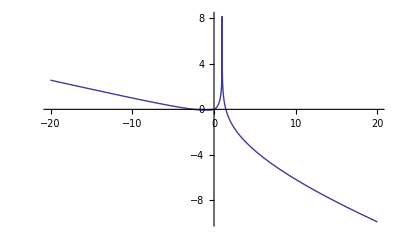

```mathematica
Plot[{Re[Gamma[aa=0,-Log[n]]],Re[Gamma[aa,0,-Log[n]]]},{n,-20,20}]
```

```mathematica
(-1)!
```

ComplexInfinity

```mathematica
Integrate[ t^(-1) E^(-t),{t,-Log[x],Infinity}]
```

ConditionalExpression[Gamma[0,-Log[x]]+Log[-Log[x]],Im[Log[x]]≠0||Log[x]<0]

```mathematica
Integrate[ (E^(-t)-1)/t,{t,0,-Log[n]}]
```

ConditionalExpression[-EulerGamma+ExpIntegralEi[Log[n]]-Log[-Log[n]],Log[n]<0]